# Preliminary feasibility calculations for NCR detection scheme

This study assumes that the key step in the detection process is the initiation of the chain reaction step. In order for the NCR approach to be viable, the chain reaction must me initiated--overwhelmingly--by Cas13 bound to its target RNA.
The concern is that the cascade may also be initiated by other contaminants in the sample, or by basal Cas13 RNAase activity. 
A simple metric that we can use to quantify the expected efficiency of different approaches is the ratio of reporter fluorescence, at steady state, that is attributable to target and background activity

```mathematica
Clear["Global`*"]
```

## Set parameter values

```mathematica
values = {konAS-> 1, koffAS-> 1, kcAS->1};
```

## System 1: Sherlock

Assume that Cas13 binds target RNA instantaneously. Allow for off-target cleavage of reporter by background contaminants, as well as unbound Cas13

#### Solve for steady-state reporter levels

```mathematica
eqA = A'[t]==-konAS * A[t] * S[t] + (koffAS + kcAS) * AS[t] ;  (* Activated Cas13-RNA complex *)
```

```mathematica
eqAS = AS'[t]==konAS * A[t] * S [t]- (koffAS + kcAS) * AS[t];
```

```mathematica
eqS = S'[t]==  -konAS * A[t] * S[t]  +koffAS*AS[t] ;
```

{konAS→1,koffAS→1,kcAS→1}

```mathematica
s = NDSolve[{eqA/.values,eqAS/.values,eqS/.values ,A[0]==1,AS[0] == 0 ,S[0]==1},{A,S,AS},{t,0,30}];
```

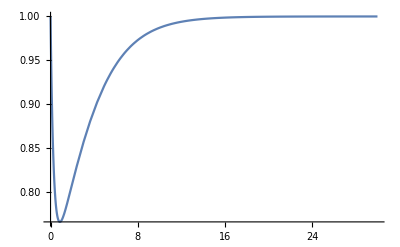

```mathematica
Plot[Evaluate[A[t]/.s],{t,0,30},PlotRange->All]
```